```mathematica
Clear[f];
f[x_]:=x^3-3x^2-5;
q=Simplify[(f[x+h]-f[x])/h]
```

h^2+3 h (-1+x)+3 (-2+x) x

```mathematica
m[x_]=Limit[q,h->0]
```

3 (-2+x) x

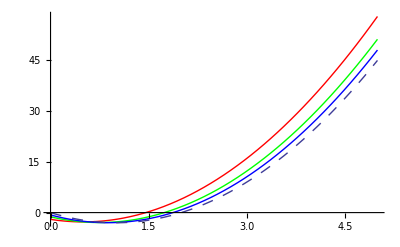

```mathematica
p1=Plot[q/.h->1,{x,0,5},
PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity];
p2=Plot[q/.h->.5,{x,0,5},
PlotStyle->RGBColor[0,1,0],DisplayFunction->Identity];
p3=Plot[q/.h->.25,{x,0,5},
PlotStyle->RGBColor[0,0,1],DisplayFunction->Identity];
p4=Plot[m[x],{x,0,5},
PlotStyle->Dashing[{.02}],DisplayFunction->Identity];
Show[{p1,p2,p3,p4},DisplayFunction->$DisplayFunction]
```

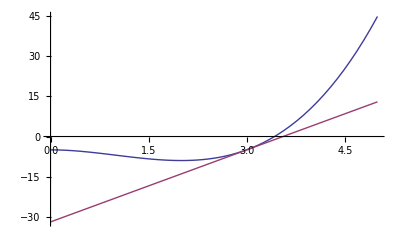

```mathematica
y=m[3](x-3)+f[3];
Plot[{f[x],y},{x,0,5}]
```

```mathematica
Table[m[x],{x,1,5,.2}]
```

{-3.,-2.88,-2.52,-1.92,-1.08,0.,1.32,2.88,4.68,6.72,9.,11.52,14.28,17.28,20.52,24.,27.72,31.68,35.88,40.32,45.}

```mathematica
Clear[f];
f[x_]=5x^3-15x-2;
f'[x]
```

-15+15 x^2

```mathematica
D[f[x],x]
```

-15+15 x^2

```mathematica
f''[x]
```

30 x

```mathematica
D[f[x],{x,3}]
```

30

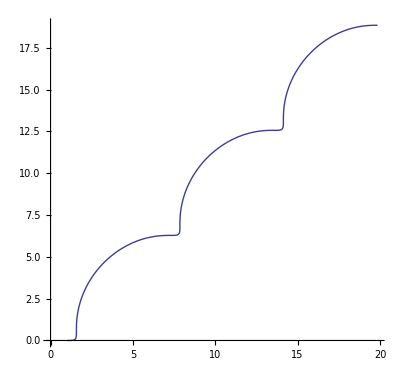

```mathematica
Clear[x,y];
x[t_]=t+Cos[t];
y[t_]=t-Sin[t];
funplot=ParametricPlot[{x[t],y[t]},{t,0,6π}]
```

```mathematica
yprime[t_]=y'[t]/x'[t]
```

(1-Cos[t])/(1-Sin[t])

```mathematica
Simplify[yprime'[t]/x'[t]]
```

(2 Sin[t/2])/(Cos[t/2]-Sin[t/2])^5

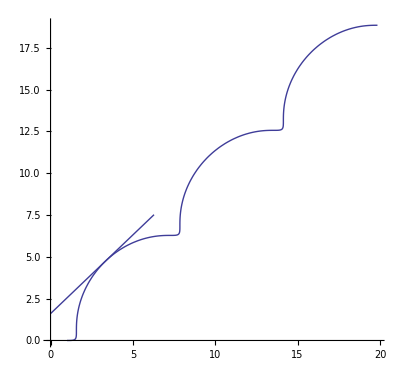

```mathematica
tanline=yprime[4](x-x[4])+y[4];
tanlineplot=Plot[tanline,{x,0,2π}];
Show[funplot,tanlineplot]
```

```mathematica
Clear[x,y,eq];
eq=(x-1)^4==x^2-y^2;
solutions=Solve[eq,y]
```

{{y→-√(-(-1+x)^4+x^2)},{y→√(-(-1+x)^4+x^2)}}

```mathematica
implicitder=Dt[eq,x]
```

4 (-1+x)^3==2 x-2 y Dt[y,x]

```mathematica
impsolution=Solve[implicitder,Dt[y,x]]
```

{{Dt[y,x]→(2-5 x+6 x^2-2 x^3)/y}}

```mathematica
impsolution/.y->solutions[[1,1,2]]
```

{{-(-4 (-1+x)^3+2 x)/(2 √(-(-1+x)^4+x^2))→-(2-5 x+6 x^2-2 x^3)/(√(-(-1+x)^4+x^2))}}

```mathematica
impsolution/.y->solutions[[2,1,2]]
```

{{(-4 (-1+x)^3+2 x)/(2 √(-(-1+x)^4+x^2))→(2-5 x+6 x^2-2 x^3)/(√(-(-1+x)^4+x^2))}}

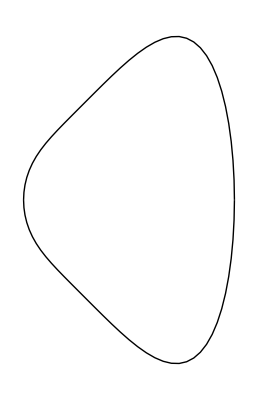

```mathematica
eqgraph=ImplicitPlot[eq,{x,-4,4}]
```

```mathematica
x0=7/4;y0=Sqrt[703]/16;
m=impsolution[[1,1,2]]/.{x->x0,y->y0}
```

29/(2 √703)

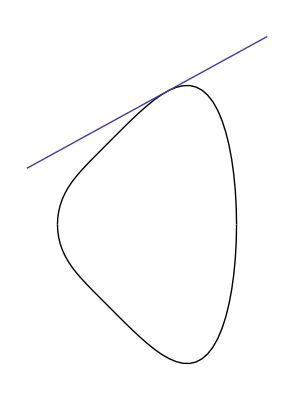

```mathematica
Clear[x,y];
y=m(x-x0)+y0;
tangraph=Plot[y,{x,0,3}];
Show[{eqgraph,tangraph}]
```